****************************************************
The potential we work out in this document has the form    V(x)=(x+A*Sin(x/f))^2.
****************************************************

```mathematica
(*Inflation Potential dependent on time and parameters*)
V[A_,f_][t_]:=(Tanh[y[A,f][t]/Sqrt[6]]+A*Sin[(Tanh[y[A,f][t]/Sqrt[6]])/f])^2;

(*Inflation Potential with only time dependence*)
V[y[t_]]=(Tanh[y[t]/Sqrt[6]]+A*Sin[(Tanh[y[t]/Sqrt[6]])/f])^2;

(*Inflation Potential without time dependence*)
Vvv[A_,f_][y_]:=(Tanh[y/Sqrt[6]]+A*Sin[(Tanh[y/Sqrt[6]])/f])^2;

(*Inflation Potential with only inflaton dependence*)
Vv[y_]:=(Tanh[y/Sqrt[6]]+A*Sin[(Tanh[y/Sqrt[6]])/f])^2;

(*Derivative of the potential with dependence only on time*)
VV[y[t]]=D[V[y[t]],y[t]];
```

```mathematica
(*Plot of the potential*)
Manipulate[Plot[Evaluate[Vvv[A,f][y]],{y,0,7},AxesLabel->{Style[φ,FontSize->20],Style["V(φ)",FontSize->20]},PlotRange->All],{{A,0.1303621},0,0.3,0.0000001},{{f,0.1295487},0.1,0.23,0.0000001}]
```

```mathematica
VvvV[A_,f_][y_]:=(Tanh[y/Sqrt[2*6]]+A*Sin[(Tanh[y/Sqrt[2*6]])/f])^2;
VvvVv[A_,f_][y_]:=(Tanh[y/Sqrt[3*6]]+A*Sin[(Tanh[y/Sqrt[3*6]])/f])^2;
```

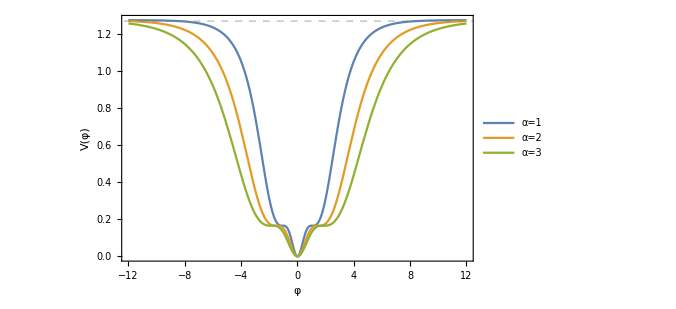

```mathematica
Plot[Evaluate[{Vvv[A,f][y],VvvV[A,f][y],VvvVv[A,f][y]}/.{A->0.130362,f->0.129548}  ],{y,-12,12},Frame->True,BaseStyle->{FontFamily->"Arial",16},PlotRange->All,GridLines->{{},{1.27}},GridLinesStyle->Directive[Gray,Dashed],FrameLabel->{"φ","V(φ)"},PlotLegends->Placed[LineLegend[{"α=1", "α=2","α=3"},LabelStyle->{GrayLevel[0.3],18},LegendLayout->{"Row",3}],{0.86,0.25}],ImageSize->500,FrameStyle->Directive[FontSize->16]]
```

Analysis Beginning

The function VVr[y[n]] is the potential divided by the derivative of the potential. This terms appears in the Klein-Gordon equation when we write it in terms of the efolding “N”.
(d^2 φ)/dN^2+3 dφ/dN- 1/(2 M^2)(dφ/dN)^3+(3 M^2-1/2(dφ/dN)^2)(d(LogV))/dφ=0

```mathematica
(*We should be careful with the number of efolds we use. For n=0 it might appear an error*)
VVr[y[n]]=D[Log[Vv[y[n]]],y[n]];

y0=5.839;                                                                   (*Initial position*)
u=-Vvvv'[y]/Vvvv[y]/.y->y0             ;       (*Initial velocity*)

(*numerically solve the KG*)
neti=ParametricNDSolve[{y''[n]+3y'[n]-1/(2)(y'[n])^3+(3-1/2(y'[n])^2)VVr[y[n]]==0,y[0]==y0,y'[0]==u},y,{n,0,100},{A,f}];

Manipulate[Plot[Evaluate[y[A,f][n]/.neti],{n,0,100},AxesLabel->{Style[Ν,FontSize->20],Style[φ[Ν],FontSize->20]},PlotRange->{{0,100},{0,7}}],{{A,0.1303621},0,0.3,0.0000001},{{f,0.1295487},0.1,0.23,0.0000001}]
```

Then we plot the velocity of inflaton against the number of efolds “φ(Ν)”

```mathematica
(*Manipulate[Plot[Evaluate[-y[A,f]'[n]/.neti],{n,0,74},AxesLabel->{Style[Ν,FontSize->20],Style[φ'[Ν],FontSize->20]},PlotRange->{{0.01,74},{0,1}}],{{A,0.1315},0,0.3,0.0001},{{f,0.131},0.1,0.23,0.0001}]*)
```

The first slow roll parameter in terms of the efolding:     ε=1/(2 Μ_p^2)(dφ/dN)^2
The planck mass is considered to be M_p=1

```mathematica
{(*A*)0.130383,(*f*)0.129576}
```

{0.130383,0.129576}

```mathematica
ee[A_,f_][n_]=1/2(y[A,f]'[n])^2;  

Manipulate[LogPlot[Evaluate[ee[A,f][n]/.neti],{n,0,90},AxesLabel->{Style[N,FontSize->26],Style[ε[Ν],FontSize->24]},PlotRange->{{0,75},{10^-12,100}},GridLines->{{38.2,55,61.5,65}, {1,10^-9.75,10^-9.5,10^-10,1*10^-11}}],{{A,0.130386},0,0.3,0.000001},{{f,0.12958},0.1,0.23,0.000001}]
```

ParametricNDSolve::mxst: Maximum number of 102328 steps reached at the point n == 60.2797.

ParametricNDSolve::ndsz: At n == 64.9773, step size is effectively zero; singularity or stiff system suspected.

ParametricNDSolve::mxst: Maximum number of 102335 steps reached at the point n == 57.6903.

```mathematica
eps[x_]:=1/2(Vv'[x]/Vv[x])^2;
eta[x_]:=(Vv''[x]/Vv[x]);
nns[x_]:=1+2eta[x]-6eps[x];
 

nns[y0]/.neti/.{A->0.130386,f->0.12958} 
y0
```

0.943015

5.839

```mathematica
16eps[y0]/.neti/.{A->0.130362,f->0.129548}
```

0.00773999

The Second slow roll parameter “η” in terms of the efolding “N”

η_H=ε_H-1/2(d(Log(ε_H)))/dN

```mathematica
hh[A_,f_][n_]=ee[A,f][n]-1/2D[ee[A,f][n],n]/ee[A,f][n]; (*The second slow roll parameter*)


g2=Manipulate[LogPlot[Evaluate[Abs[eee[A,f][n]/.neti]],{n,0,70},AxesLabel->{Style["N",FontSize->26],Style["η(Ν)",FontSize->24]},PlotRange->{{0,65},{10^-10,10}},GridLines->{{-1,0,0.6},{0,0.06,{Dashed,Thick,Blue}}}],{{A,0.131457},0,0.3,0.000001},{{f,0.130947},0.1,0.23,0.000001}]
```

```mathematica
eee[A_,f_][n_]=D[Log[ee[A,f][n]],n];

Manipulate[LogPlot[Evaluate[Abs[eee[A,f][n]/.neti]],{n,0,2},AxesLabel->{Style["N",FontSize->26],Style["η(Ν)",FontSize->24]},PlotRange->{{0,2},{10^-10,10}},GridLines->{{-1,0,0.6},{0,0.06,{Dashed,Thick,Blue}}}],{{A,0.132093},0,0.3,0.0000001},{{f,0.131721},0.1,0.23,0.0000001}];
```

Next what we want to do is to calculate H(N). The relation we use is H^2 =1/(3 M^2)(V+(φ̇)^2/2)=> H=((V(φ(Ν)))/(3 Μ_p^2-1/2(dφ/dN)^2))^(1/2)
But we see that first we need to express the potential V(φ) in terms of N. Thus:

```mathematica
Vvvv[y_]:=V0*(Tanh[y/Sqrt[6]]+A*Sin[(Tanh[y/Sqrt[6]])/f])^2/.{A->0.130349,f->0.1295308} ; 
ren=Solve[1/(24Pi^2ee[0.1315,0.131][0]/.neti)Vvvv[y0]==2.2*10^-9,V0] (*CMB Compatibility*)
```

ParametricNDSolve::ndsz: At n == 63.1285, step size is effectively zero; singularity or stiff system suspected.

{{V0→2.04657×10^-10}}

```mathematica
Vvvv[A_,f_][n_]=(Tanh[y[A,f][n]/Sqrt[6]]+A*Sin[(Tanh[y[A,f][n]/Sqrt[6]])/f])^2;


Hhh[A_,f_][n_]=Sqrt[V0*Vvvv[A,f][n]/(3-1/2y[A,f]'[n]^2)];


Manipulate[Plot[Evaluate[Hhh[A,f][n]/.neti/.ren],{n,0,65},AxesLabel->{Style["N",FontSize->26],Style["H(Ν)",FontSize->24]},PlotRange->All],{{A,0.131457},0,0.3,0.000001},{{f,0.130947},0.1,0.23,0.000001}]
```

ParametricNDSolve::ndsz: At n == 61.7907, step size is effectively zero; singularity or stiff system suspected.

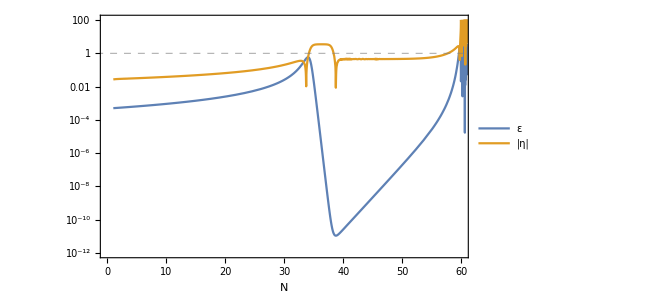

```mathematica
LogPlot[Evaluate[{ee[A,f][n],Abs[hh[A,f][n]]}/.neti/.ren/.{A->0.130362,f->0.129548}  ],{n,1,69},Frame->True,BaseStyle->{FontFamily->"Arial",15},PlotRange->{{0,60},{10^-12,100}},ImageSize->495,GridLines->{{},{1}},GridLinesStyle->Directive[Gray,Dashed],FrameLabel->{"N",""},GridLinesStyle->Directive[Gray,Dashed],FrameLabel->{"N",""},PlotLegends->Placed[LineLegend[{"ε", "|η|"},LabelStyle->{GrayLevel[0.3],18},LegendLayout->{"Row",2}],{0.92,0.25}],ImageSize->Full]
```

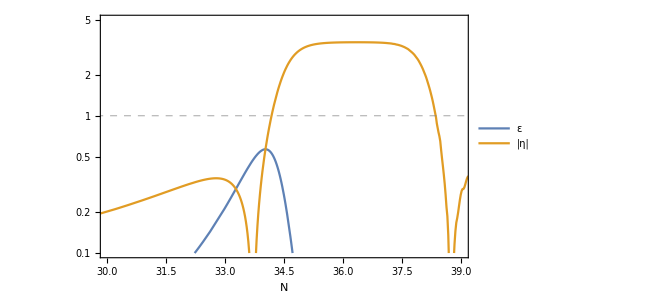

```mathematica
LogPlot[Evaluate[{ee[A,f][n],Abs[hh[A,f][n]]}/.neti/.ren/.{A->0.130362,f->0.129548}  ],{n,1,69},Frame->True,BaseStyle->{FontFamily->"Arial",15},PlotRange->{{30,39},{10^-1,5}},ImageSize->495,GridLines->{{},{1}},GridLinesStyle->Directive[Gray,Dashed],FrameLabel->{"N",""},PlotLegends->Placed[LineLegend[{"ε", "|η|"},LabelStyle->{GrayLevel[0.3],18},LegendLayout->{"Row",2}],{0.85,0.25}],ImageSize->Full]
```

Then we manipulate-plot the Power Spectrum P(N) using the EXACT first leading order formula: P(N)=1/(8 π^2 M_p^2)H^2/(ε(N))

```mathematica
P[A_,f_][n_]=Hhh[A,f][n]^2/(8Pi^2*ee[A,f][n]);

Manipulate[LogPlot[Evaluate[P[A,f][n]/.neti/.ren],{n,0,65},AxesLabel->{Style["N",FontSize->26],Style["P(Ν)",FontSize->24]},PlotRange->{{0,65},{1,10^-14}},GridLines->{{39.5},{1,10^-4,10^5,10^6,10^(-12)}}],{{A,0.131457},0,0.3,0.0000001},{{f,0.130947},0.1,0.23,0.0000001}]
```

METHOD No1: we already have calculated the exact form of P(N) and we do the replacement n->Log[k/0.05]+N_60. From this formula we have assumed that (H(N))/(H_*)~1 which is a good approximation. This replacement comes from k=k_*(H(N))/(H_*)e^(N-N_*)

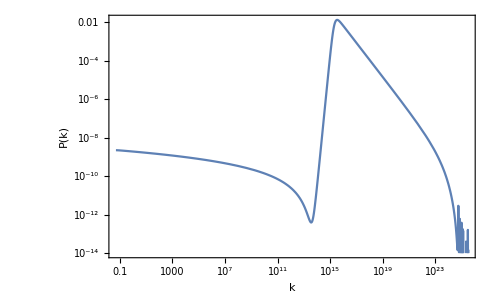

```mathematica
LogLogPlot[Evaluate[(P[A,f][n]/.n->Log[k/0.05]+0)/.neti/.ren/.{A->0.130362,f->0.129548}   ],{k,0.05Exp[0-0],0.05Exp[70-0]},Frame->True,FrameLabel->{"k","P(k)"},BaseStyle->{FontFamily->"Arial",20},PlotRange->{{10^27,10^-2},{10^-14,10^-1}},ImageSize->495,GridLines->{{6*10^15,10^13},{1,{10^-2,{Dashed,Thick,Blue}},{10^-9,{Dashed,Thick,Orange}},10^-3}}]
```